```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];

Import["model/data.wl"];
Import["model/plot-utils.wl"];
Import["model/model.wl"];
```

```mathematica
state="CA";

params=stateParams[state,pC0,pH0,medianHospitalizationAge0,ageCriticalDependence0,ageHospitalizedDependence0];
icuCapacity=params["icuBeds"]/params["population"];
thisStateData=Select[parsedData,(#["state"]==state&&#["positive"]>0)&];
hospitalCapacity=(1-params["bedUtilization"])*params["staffedBeds"]/params["population"];
hospitalizationData = stateHospitalizationData[state];
```

```mathematica
distance[t_] := stateDistancing[state,scenario1,t];
sol=CovidModelFit[
daysUntilNotInfectiousOrHospitalized0,
daysFromInfectedToInfectious0,
daysUntilNotInfectiousOrHospitalized0,
daysToLeaveHosptialNonCritical0,
pPCRNH0,
pPCRH0,
daysTogoToCriticalCare0,
daysFromCriticalToRecoveredOrDeceased0,
fractionOfCriticalDeceased0,
importlength0,initialInfectionImpulse0,
tmax,
params["pS"],
params["pH"],
params["pC"],
distance,
icuCapacity
]
model[r0natural_,importtime_][i_,t_]:=Through[sol[r0natural,importtime][t],List][[i]]/;And@@NumericQ/@{r0natural,importtime,i,t}
```

ParametricFunction[<>]

```mathematica
longData=Select[Join[{1,#["day"],If[TrueQ[#["deathIncrease"]==Null],0,(#["deathIncrease"]/params["population"])//N]}&/@thisStateData,
{2,#["day"],(#["positiveIncrease"]/params["population"])//N}&/@thisStateData
],#[[3]]>0&];
```

```mathematica
dataWeights=((params["population"]#[[3]])^-.5)&/@longData;
fit=NonlinearModelFit[
longData,
model[r0natural,importtime][i,t] - model[r0natural,importtime][i,t-1],
{{r0natural, Log[r0natural0]}, {importtime, Log[params["importtime0"]]}},
{i,t},
Weights -> dataWeights,
AccuracyGoal->5,
PrecisionGoal->10
];
```

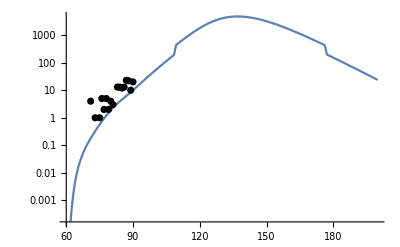

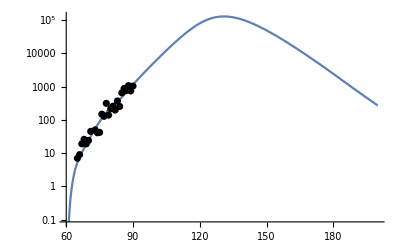

```mathematica
Show[
LogPlot[{params["population"]fit[1,t]},{t,60,200}],
ListLogPlot[{
{#["day"],#["deathIncrease"]}&/@thisStateData
},PlotStyle->Black]
]
Show[
LogPlot[{params["population"]fit[2,t]},{t,60,200}],
ListLogPlot[{
{#["day"],#["positiveIncrease"]}&/@thisStateData
},PlotStyle->Black]
]
```

```mathematica
Mean[(fit["FitResiduals"]/longData[[All,3]])^2]^.5
```

0.502344

```mathematica
i1=(#[[1]]==1)&/@longData;
i2=!#&/@i1;
Mean[
Pick[(fit["FitResiduals"])^2,i1]]^.5
Mean[
Pick[(fit["FitResiduals"])^2,i2]]^.5

Mean[
Pick[(fit["FitResiduals"]/longData[[All,3]])^2,i1]]^.5
Mean[
Pick[(fit["FitResiduals"]/longData[[All,3]])^2,i2]]^.5

(Total[#^2])&[Pick[fit["FitResiduals"],i1]]/(Total[(#-Mean[#])^2])&[Pick[fit["Response"],i1]]
(Total[#^2])&[Pick[fit["FitResiduals"],i2]]/(Total[(#-Mean[#])^2])&[Pick[fit["Response"],i2]]
```

1.92039×10^-7

2.97653×10^-6

0.622416

0.400641

1.07291

0.118899